```mathematica
<<"/Users/noahsteinberg/Desktop/BNV_Mathematica_Programs/RunDec.m"
```

RunDec: a Mathematica package for running and decoupling of the

strong coupling and quark masses

by K.G. Chetyrkin, J.H. K\"uhn and M. Steinhauser (January 2000)

by F. Herren and M. Steinhauser (April 2016, v2.1)

```mathematica
ALLQCD[MZ_, mb_, p0_, as5MZ_]:= Module[{as5mb, as4mb, as4p0},
as5mb=AlphasExact[as5MZ,MZ,mb,5,4];
as4mb = DecAsDownMS[as5mb, mb, mb, 4, 4];
as4p0 = AlphasExact[as4mb, mb, p0, 4, 4];
Return[(as4p0/as4mb)^(6/25)(as5mb/as5MZ)^(6/23)((as4p0 + (50π)/77)/(as4mb + (50π)/77))^(-2047/11550)((as5mb + (23π)/29)/(as5MZ + (23π)/29))^(-1375/8004)];]
ALRQCD[MZ_, mb_, p0_, as5MZ_]:= Module[{as5mb, as4mb, as4p0},
as5mb=AlphasExact[as5MZ,MZ,mb,5,4];
as4mb = DecAsDownMS[as5mb, mb, mb, 4, 4];
as4p0 = AlphasExact[as4mb, mb, p0, 4, 4];
Return[(as4p0/as4mb)^(6/25)(as5mb/as5MZ)^(6/23)((as4p0 + (50π)/77)/(as4mb + (50π)/77))^(-173/825)((as5mb + (23π)/29)/(as5MZ + (23π)/29))^(-430/2001)];]
```

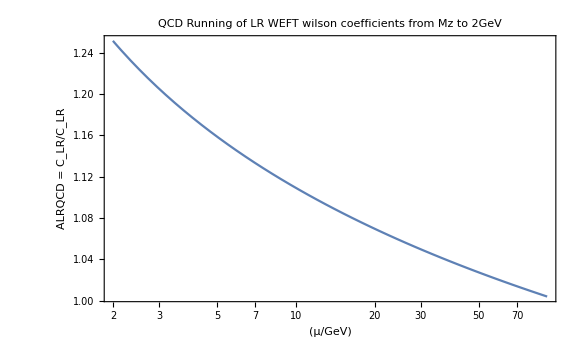

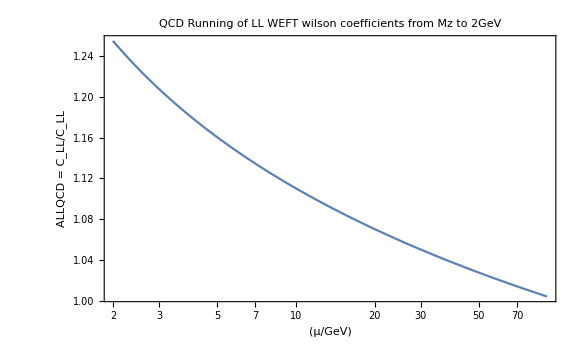

```mathematica
LR = LogLinearPlot[ALRQCD[91.1876, 4.18, p, 0.1185], {p, 2.0, 91.1876}, Frame->True, FrameLabel->{"(μ/GeV)", "ALRQCD = C_LR/C_LR"}, PlotLabel->"QCD Running of LR WEFT wilson coefficients from Mz to 2GeV"]
LL =LogLinearPlot[ALLQCD[91.1876, 4.18, p, 0.1185], {p, 2.0, 91.1876}, Frame->True, FrameLabel->{"(μ/GeV)", "ALLQCD = C_LL/C_LL"}, PlotLabel->"QCD Running of LL WEFT wilson coefficients from Mz to 2GeV"]
```

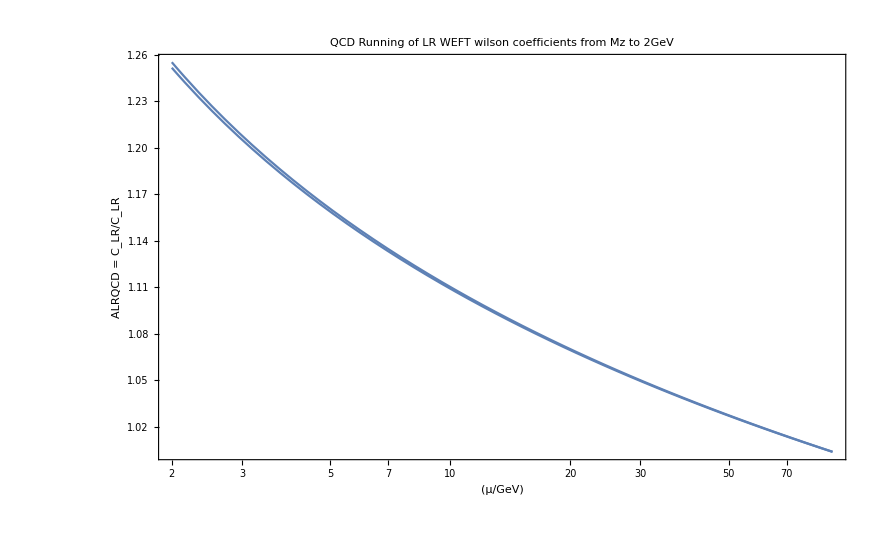

```mathematica
Show[LR, LL, PlotRange->Automatic]
```

```mathematica
ALRQCD[91.1876, 4.18, 2.0, 0.1185]
```

1.25161

```mathematica
ALLQCD[91.1876, 4.18, 2.0, 0.1185]
```

1.25518